```mathematica
ClearAll[z];
logkC1:=-6;
O20:=0.3;
H0:=70;
kC1:=10^(logkC1+3);
O10:=1-O20;
t0:=1/H0;
f[x_]=NDSolveValue[{z''[t]==(H0^4*kC1*O10^2*(z[t]^4+1)+3*H0^4*O10^2*z[t]^2*(2*kC1-3*z'[t])+H0^4*O10^2*z[t]^3*(4*kC1-3*z'[t])-3*H0^4*O10^2*z'[t]+5*H0^2*O10*z'[t]^3-kC1*z'[t]^4+H0^2*O10*z[t]*(4*H0^2*kC1*O10-9*H0^2*O10*z'[t]+5*z'[t]^3))/(2*H0^2*O10*(1+z[t])^2*z'[t]),z[t0]==0,z'[t0]==-H0},z[x],{t,t0,0}]
```

NDSolveValue::ndsz: 在 t == 0.000513718 处，步长实际上为零；可能存在奇点或者刚性系统.

InterpolatingFunction[…][x]

InterpolatingFunction::dmval: 输入值 {2.91837×10^-7} 位于插值函数的数据范围之外. 将使用外推法.

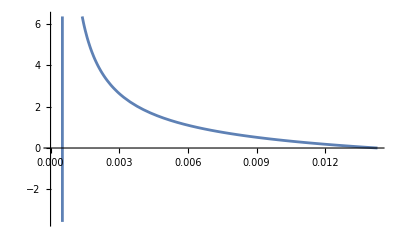

```mathematica
Plot[
f[x],{x,0,t0}]
```

InterpolatingFunction::dmval: 输入值 {2.91545×10^-7} 位于插值函数的数据范围之外. 将使用外推法.

General::stop: 在本次计算中，InterpolatingFunction::dmval 的进一步输出将被抑制.

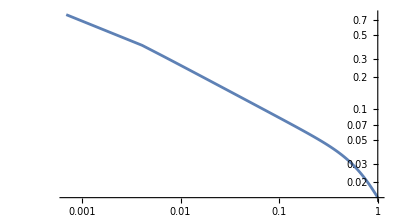

```mathematica
a[x_]=1/(1+f[x]);
ParametricPlot[{a[x],-1/(f'[x]*a[x]^3)},{x,0,t0},ScalingFunctions->{"Log","Log"},PlotRange->All]
```